{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{{x→1/2 (1-√3),y→1/2 (-1-√3)},{x→1/2 (1+√3),y→1/2 (-1+√3)}}

{{x→1/2 (1-√3),y→1/2 (-1-√3)},{x→1/2 (1+√3),y→1/2 (-1+√3)}}

{1/2 (1-√3),1/2 (1+√3)}

{}

{{}}

{{x→-1},{x→1},{x→4}}

{{x→-1.41421},{x→1.},{x→1.41421}}

{x→-0.588533}

{x→-0.588533}

{x→-0.588533}

{x→1.41421}

{x→1.}

{x→0.69314718055994530941723}

-1<x<1&&-√(1-x^2)<y<√(1-x^2)

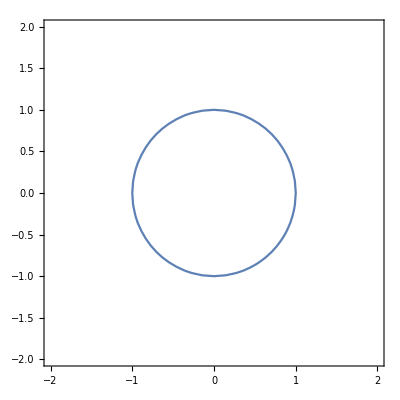

{{y→Function[{x},ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])]}}

{{y→Function[{x},-1/2 a ⅇ^-x (-1+ⅇ^x Cos[x]-ⅇ^x Sin[x])]}}

{{y→InterpolatingFunction[…]}}

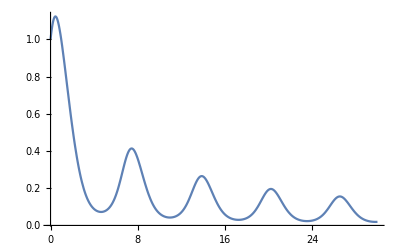

ψ^(2,0)[x,t]==-(ψ^(0,2)[x,t])/α^2

{{ψ[x,t]→C[1][t+(x √(-α^2))/α^2]+C[2][t-(x √(-α^2))/α^2]}}

```mathematica
Solve[a*x^2+ b*x + c == 0, x]
Solve[x^2+y^2 == 2 && x-y ==1 , {x,y}]
sol = Solve[x^2+y^2 == 2 && x-y ==1 , {x,y}] 
x/.sol
Solve[x == 1&& x==2, x]
Solve[x ==x,x]
Solve[(x^4-1)*(x-4) == 0,x,Reals]
NSolve[(x-1)*(x^4-4) == 0, Reals]
FindRoot[Sin[x] + Exp[x], {x,0}]
FindRoot[Sin[x] + Exp[x], {x,0,1}]
FindRoot[Sin[x]+ Exp[x], {x,0,-1,1}]
FindRoot[x^2-2,{x,1}]
FindRoot[x^2-x, {x,1}, WorkingPrecision-> 60]
Needs["FunctionApproximations`"]
InterpolateRoot[Exp[x]== 2 , {x,0,1}]
Reduce[x^2+y^2 < 1, {x,y}]
ContourPlot[x^2+y^2 == 1, {x,-2,2},{y,-2,2}]
DSolve[{y'[x]+ y[x] == a Sin[x ]},y,x]
DSolve[{y'[x]+ y[x] == a Sin[x ], y[0] == 0},y,x]
s = NDSolve[{y'[x]==y[x]*Cos[x+y[x]],y[0]==1},y,{x,0,30}]
Plot[Evaluate[y[x] /.s],{x,0,30},PlotRange->All]
eq = D[ψ[x,t],{x,2}]==-1/α^2 D[ψ[x,t],{t,2}]
DSolve[eq, ψ[x,t],{x,t}]
```